# Abstract Theory for the Foundations of Medicine

# Metamodeling the Foundations of Medicine

# The Foundations of Medicine: A Minimal Abstract View

# A Formalized Theory of the Foundations of

# Is There a Generalized Theory of the Foundations of Medicine?

# Towards a Generalized Theory for the Foundations of Medicine?

# Approaching the Foundations of Medicine through the Computational Paradigm

# Towards a Formalized Theory of Medicine

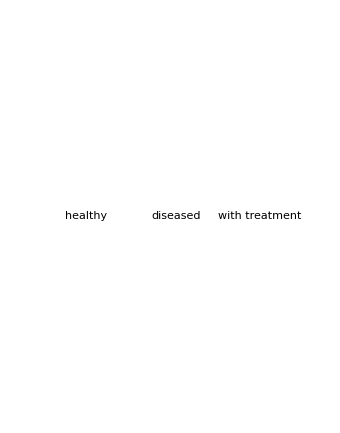

```mathematica
GraphicsRow[{Labeled[ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]},ImageSize->{Automatic,400}],"healthy"],Labeled[SeedRandom[234242];PlotCA[PerturbCA[{getca[#,110],#},"NRandom"->1],ImageSize->{Automatic,400}]&[{299459058088077823758143088095350287424,4,1}],"diseased"],Labeled[SeedRandom[434242];PlotCA[PerturbCA[{getca[#,110],#},"NRandom"->1],ImageSize->{Automatic,400}]&[{299459058088077823758143088095350287424,4,1}],"with treatment"]}]
```

## A Theory of Medicine?

As it’s now practiced medicine is almost always about particulars: “this has gone wrong; this is how to fix it”.  But is it possible to talk about medicine in a more general, abstract way?  And to discuss its essential features and phenomena without getting enmeshed in all the details.

My goal here is to take the first steps in creating a formalized theory of medicine.  I should make it clear at the outset that I’m not trying to make a specific model of particular mechanisms and characteristics in biological systems.  Rather, my purpose is to “zoom out” and create what one can think of as a “metamodel” that captures the general, abstract features of what’s going on, and with in one can explore---and discover---essential phenomena relevant to the foundations of medicine.

What I’ll do here builds on my recent work on using the computational paradigm to create a metamodel of biological evolution.  And indeed I’ll use the very same class of simple computational models for organisms.  But now---instead of looking at the effects of idealized genetic mutations---I’m going to look at individual types of “evolved organisms”, and see what perturbations do to them.  The idea is that “healthy” behavior is what happens without perturbations; the perturbations induce “disease”.  And in these terms one can think of the “fundamental problem of medicine” as being to find additional perturbations that can be imposed to “treat the disease” and return the organism to behavior that achieves at least similar “fitness” to the “healthy” case.

As we’ll see, our perturbations can lead to all sorts of detailed changes in the behavior of our idealized models, much like perturbations in biological systems can lead to vast numbers of changes, say at the molecular level.  But, as in medicine, we can imagine that all we can observe are coarse-grained “symptoms” (or the results of coarse-grained tests).  And then the challenge is to work out from these symptoms what “treatment” (if any) will end up being needed or useful.

I should emphasize again that the approach I’m taking is based on a metamodel that’s abstracted far away from the specific actualities of biology and medicine.  But what we’ll discover is that many essential phenomena are at their core purely computational---so we can expect them to robust apply not only to our metamodel but also in actual biological and medical situations. But one thing that’s important is that the metamodel itself is computationally quite explicit and concrete.  And that means we can run all sorts of experiments on it---and get definite (if often surprising) results---that we can use to structure our thinking and build our intuition about the foundations of medicine.

## A Minimal Metamodel

Our minimal metamodel is going to be based on very simple (cellular automaton) computational systems that we can think of as growing, developing and (usually) eventually dying.   The system has definite rules---that we can think of as being like its genome---that in the absence of perturbations determine everything it does.

Here’s an example---in which we start from a single red cell, then progress down the page by repeatedly applying the rules on the right to determine the colors of successive cells:

Arrange rules differently

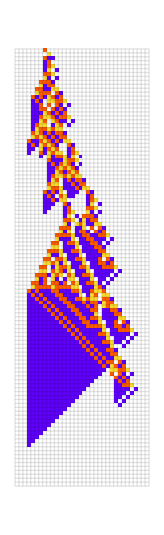
{-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]},ImageSize->{Automatic,400},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]}
```

It’s worth emphasizing that this isn’t intended to be a realistic model of any particular biological system (even though the pattern we see has a somewhat “organic” look to it).  The point instead here is just to capture in this simple computational system enough of the essence of biological systems that we can explore the foundational questions we’re interested in.

So as a first example, let’s see what happens if we perturb our system in several different ways, by randomly changing the color of the single indicated cell:

Find an actual “tumor” case
Make the arrows stand out better

Willem Note:

Actually no true cancer for Mardi Gras:

```mathematica
cps = getcancerperts[ru, "Steps"->500];
```

```mathematica
Length[cps]
```

0

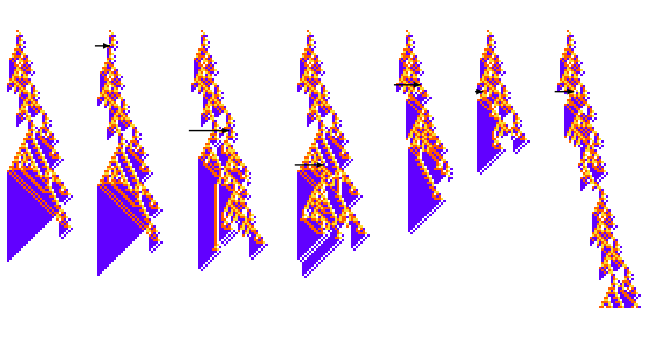

```mathematica
GraphicsRow[With[{ru={299459058088077823758143088095350287424,4,1}},Prepend[Table[PlotCA[SeedRandom[424324+i];PerturbCA[{getca[ru,120],ru},"NRandom"->1],ImageSize->{Automatic,400}],{i,{32,2,40,26,33,35}}],PlotCA[ru,"steps"->120,ImageSize->{Automatic,400}]]]]
```

#### Willem code

Made compatible with code-08, arrows come from larger side now, maybe lighten colors like so?

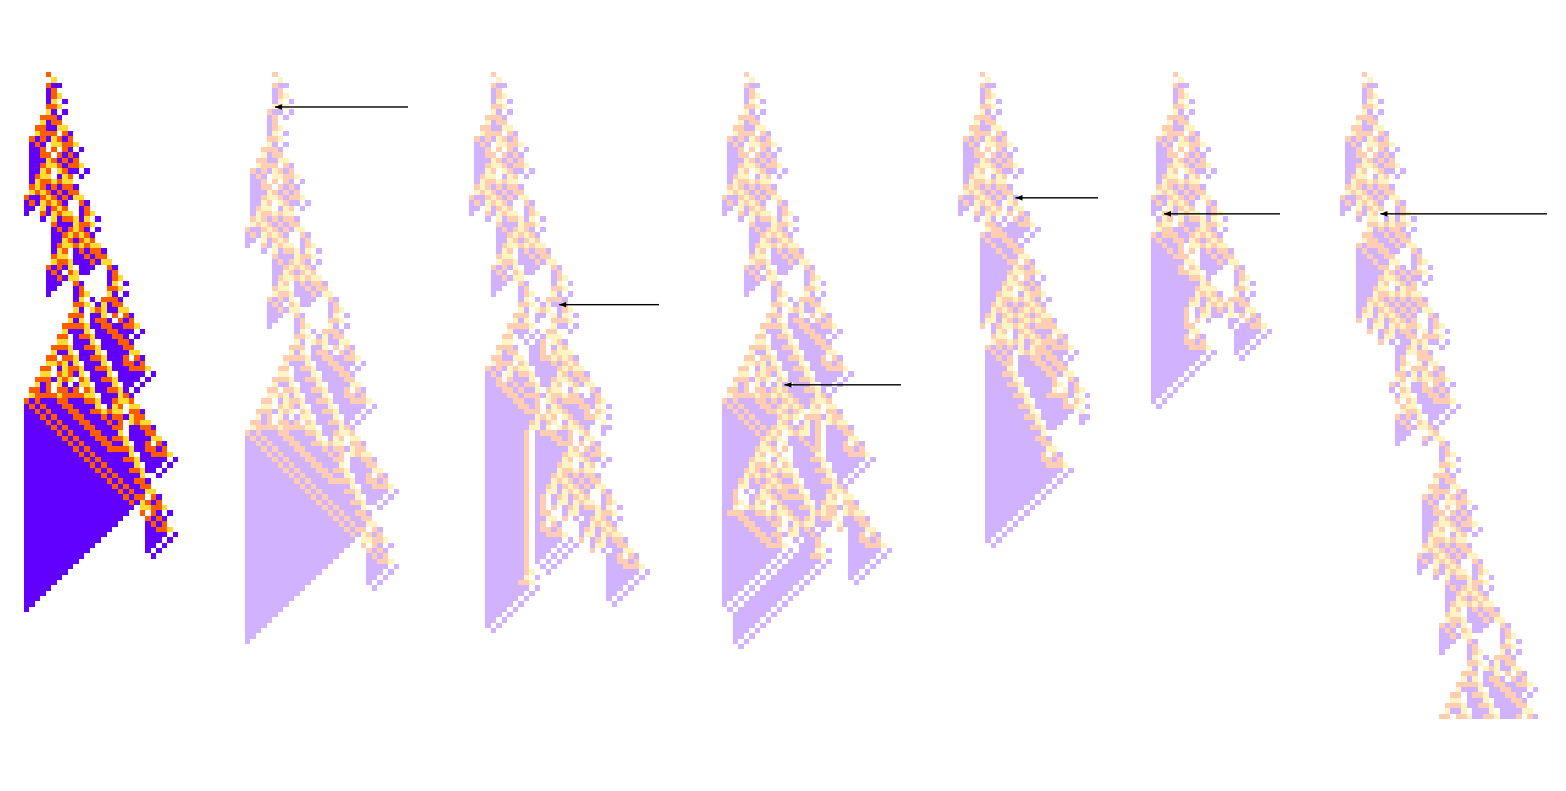

```mathematica
GraphicsRow[With[{ru={299459058088077823758143088095350287424,4,1}},Prepend[Table[PlotCA[SeedRandom[424324+i];PerturbCA[ru, "Steps"->120],ImageSize->{Automatic,400}, ColorRules->(#1->Lighter[#2, .7]&@@@ colorrules)],{i,{32,2,40,26,33,35}}],PlotCA[ru,"Steps"->120,ImageSize->{Automatic,400}]]]]
```

HighlightPerturbations

```mathematica
GraphicsRow[With[{ru={299459058088077823758143088095350287424,4,1}},Prepend[Table[HighlightPerturbations[SeedRandom[424324+i];PerturbCA[ru, "Steps"->120],ImageSize->{Automatic,400}],{i,{32,2,40,26,33,35}}],PlotCA[ru,"Steps"->120,ImageSize->{Automatic,400}]]]]
```

-Graphics-

Plot differences?

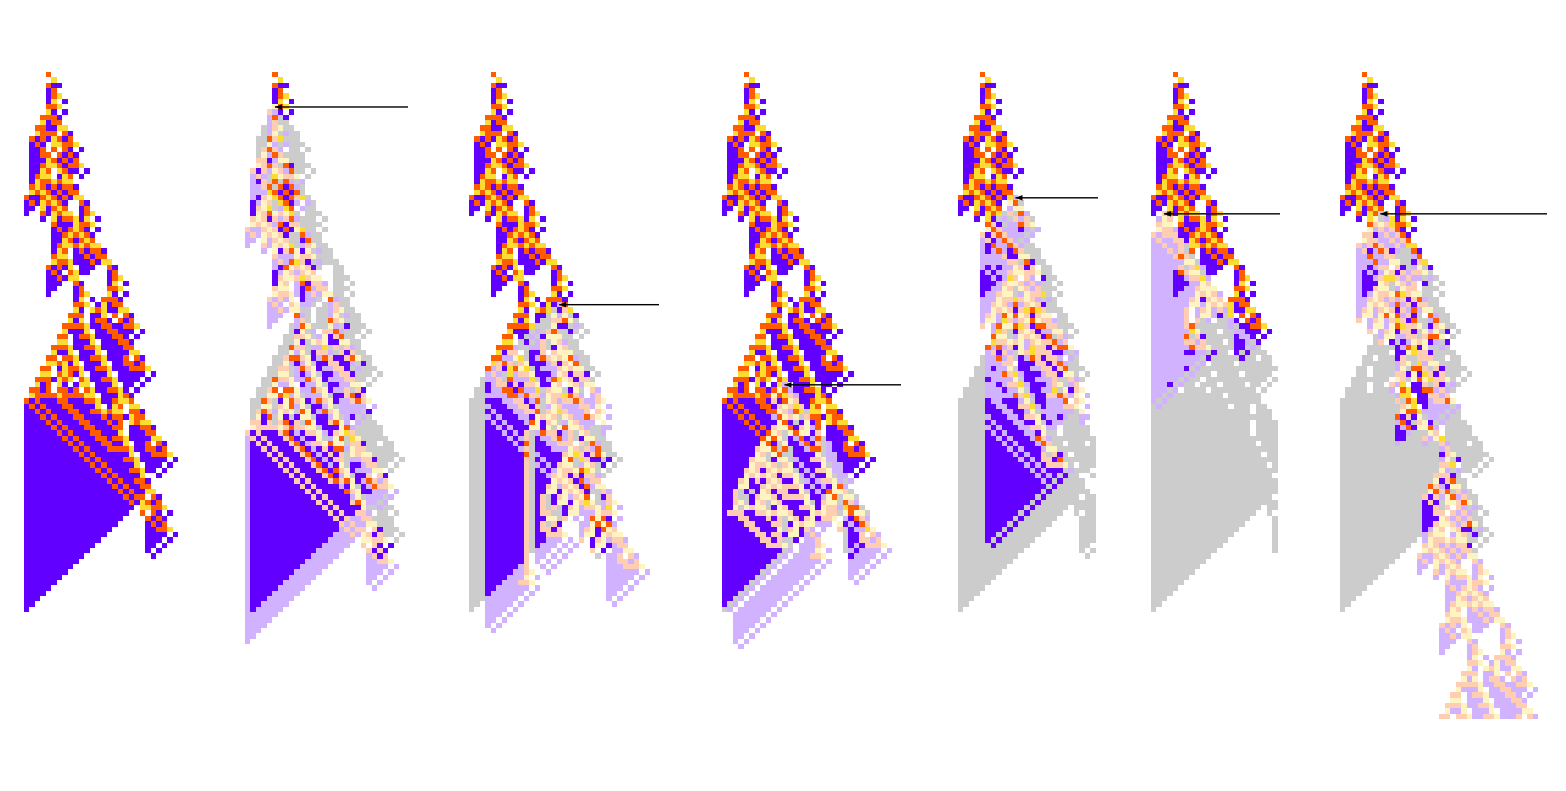

```mathematica
GraphicsRow[With[{ru={299459058088077823758143088095350287424,4,1}},Prepend[Table[PlotDifferences[SeedRandom[424324+i];ru,1, "Steps"->120,ImageSize->{Automatic,400}],{i,{32,2,40,26,33,35}}],PlotCA[ru,"Steps"->120,ImageSize->{Automatic,400}]]]]
```

TODO: Magnification

In many cases we see at least certain level of robustness.  And for example in the second case the pattern in effect quickly “heals” itself.  In the next two cases, the detailed pattern is different, but the overall structure---and lifetime---is similar.  Meanwhile, in the next two cases, the perturbations end up making the patterns “die out before their time”.  And in the final case, the pattern becomes “tumor-like”, [[growing larger forever]].

In a biological analogy, the “perturbations” we’ve introduced are intended to represent things that happen to an organism in the course of its life.  Usually the perturbations will have some effect on the organism---as indicated by the changes in patterns we see here.  Some of the time the perturbation won’t really “hurt the organism”---and it’ll “live out its natural life” and behave in more or less the same way as it would have done without the perturbation.  But in other cases, the perturbation will somehow “destabilize” the organism, in effect “giving it a disease”, and leading it for example to “die before its time”.

But now the question that’s analogous to the fundamental problem of medicine is: given some perturbation which has had a deleterious effect, can we find subsequent perturbations to apply later that will “treat” the organism, and somehow overcome the deleterious effect?

[[[ Here are some examples of how we can “treat” our organism after it “suffered” one of the perturbations above ]]]

XXXXXXX

As we’ll explain later, these “treatments” we found by analyzing complete, detailed patterns of cells.  But in medicine we don’t get to analyze things in that much completeness and detail.  Instead, all we usually have are much more coarse-grained descriptions XXXXXXXX  descriptions of

Blurred patterns ; outlines ; etc.   [convex hulls]  < Feature extraction >

[[ Computational irreducibility ;;;; why is medicine possible? ]]

## The Categorization of Disease

[[[ Generate all perturbation results ]]]

#### Willem code

By hand:

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

Fancier way

```mathematica
s = PerturbationSensitivities[{299459058088077823758143088095350287424,4,1}, "PerturbationFunction"->PerturbAll, "SensitivityFunction"-> (TestCALifeTime/@ #2&)];
```

idx and values for each color

```mathematica
s[[;;3]]
```

<|{1,201}→{0,1,100},{2,202}→{1,102,2},{3,201}→{4,5,30}|>

[[ lifetime distribution ]]     [ lifetime distribution contingent on certain symptoms ]

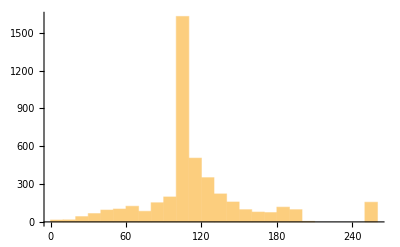

```mathematica
Histogram[lts/.-Infinity->250, 30, PlotRange->All]
```

```mathematica
With[{lt = TestLifetime[{299459058088077823758143088095350287424,4,1}]},PlotSensitivities[{299459058088077823758143088095350287424,4,1}, Max[Abs[lt - #]]&/@ s, "Steps"->120]]
```

-Graphics-

[[ Cluster them after symptom extraction ]]

## Prediction of Disease Course / Monitoring for Disease

<< How can you tell from coarse measurements whether a perturbation happened, and how bad it will be? >>

#### Willem Code

```mathematica
shapes = Map[nonzeroRange, pcas, {2}];
```

```mathematica
widths = Map[If[# == {}, 0,Abs[ Subtract@@#]+1]&,  shapes, {2}];
```

```mathematica
scs = ReverseSort[Counts[shapes]];
```

The long tail of diseases

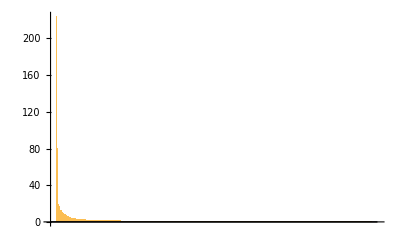

```mathematica
BarChart[scs]
```

Going to make function that plots these shapes using graphics

[[[ Can we use AI ? ]]]

## The Effect of Genetic Diversity

[[[ same analyses; different genomes ]]]

## Biological Evolution and the Origin of Our Model Organism

[[ Could be whole organism, or could be e.g. an organ ]]

Picture with  ... nn ...  between breakthroughs

```mathematica
First/@SplitBy[%,Last]
```

{{{0,4,1},0},{{633825300114114700748351602688,4,1},1},{{81763463720033458689778626068480,4,1},2},{{81763463720033458694315185274880,4,1},3},{{81931838076027891908402867077120,4,1},4},{{25967407559121214387661469853159531584,4,1},5},{{25967732077674872814392756608807478336,4,1},6},{{27320406588562325247900243404649442368,4,1},7},{{107074019143647262706119627567490706496,4,1},9},{{128341667036591835415448371735208438848,4,1},12},{{128341667026688315101165329536015445056,4,1},14},{{44247419788783520337962930866412350528,4,1},15},{{44247419788783520337962930866680785984,4,1},37},{{44247257529506691124599539288670497856,4,1},38},{{44247262600109092037517145275483319360,4,1},40},{{44247262614964372508941708574272810048,4,1},49},{{44247282897373976160612132521524096064,4,1},60},{{214388466357843207892299436237408201792,4,1},68},{{214388466357843207892299436237408234560,4,1},84},{{299459058088077823758143088095350287424,4,1},101}}

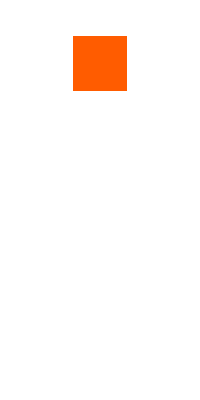
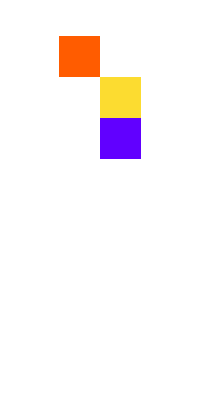
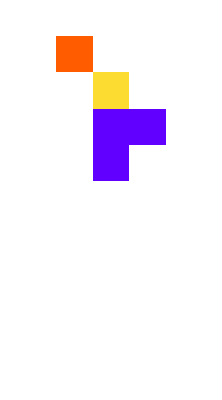
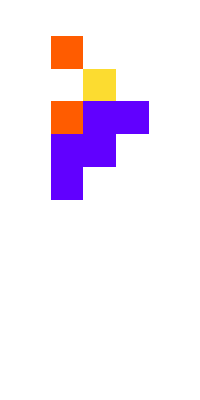
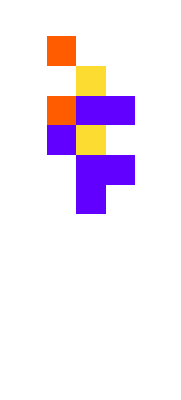
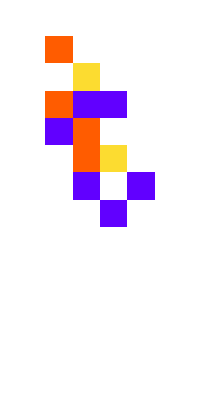
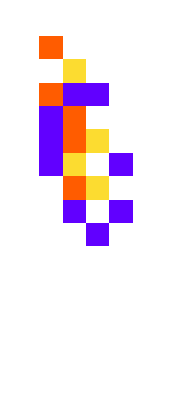
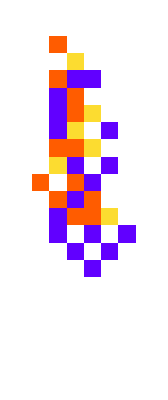
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[First[#],"Trim"->{1,5}]&/@
```

## Mechanism in Biology and Medicine

## Other Rules

## The Concept of “Symptoms”

## The Concept of Treatment

#### Willem Code

```mathematica
cancerperts = getcancerperts[ru];
```

```mathematica
healed = HealCA[ru, cancerperts[[10]], All];
```

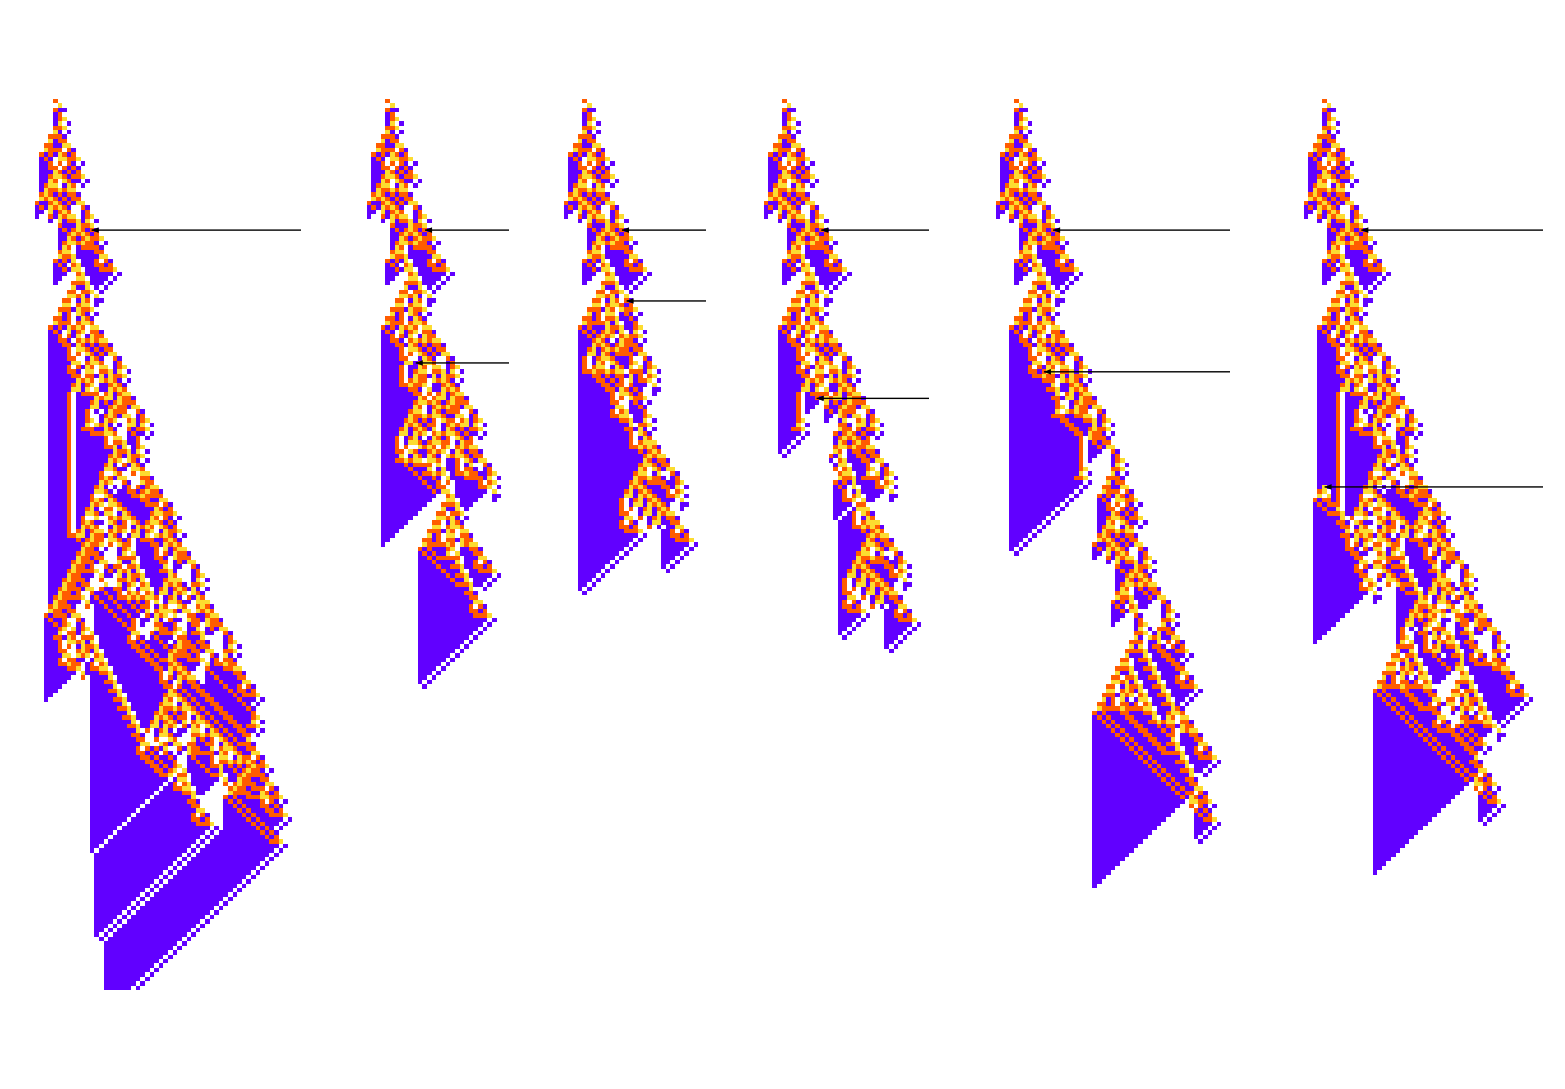

```mathematica
SeedRandom[333888];
GraphicsRow[Join[{PlotCA[PerturbCA[ru, cps[[10]], "ReturnPerturbations"->True]]},PlotCA/@ RandomSample[healed, 5]] ]
```

## “AI Medicine”

Using neural nets to go from symptoms to treatments....

<<< How much better can one get in treatment if one has more data >>>